```mathematica
f[x_]:= Sqrt[x]-2*Cos[x]
```

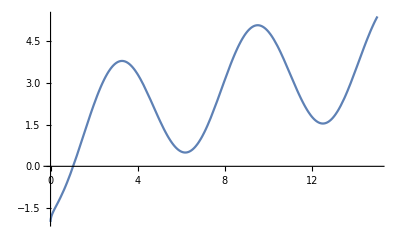

```mathematica
Plot[f[x], {x, 0, 15}]
```

```mathematica
eps = 0.00001;T={{0.5, f[0.5]}, {1, N[f[1]]},{1.5 ,f[1.5]}};ep = 1;n=1;
```

```mathematica
ex = 1;
```

```mathematica
While[ep > eps,
p = InterpolatingPolynomial[T,x];
res = Solve[p==0,x];
x1=x/.res[[2]];
ep = Abs[ex-x1];
T1 = Rest[T];
ex=x1;
T = Append[T1, {x1,N[f[x1]]}];
Print["xi = " ,x1, " eps_i = " ,ep, " i = ", n];
n=n+1]
```

xi = 1.03756 eps_i = 0.0375589 i = 1

xi = 1.03667 eps_i = 0.000886803 i = 2

xi = 1.03667 eps_i = 1.74463×10^-6 i = 3

```mathematica
Print["xi = " ,x1, " eps_i = " ,ep, " i = ", n];
```

xi = 1.03667 eps_i = 1.74463×10^-6 i = 4

```mathematica
Print[n]
```

4

```mathematica
ep
```

1.74463×10^-6

```mathematica
NSolve[f[x]==0,x]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[√x-2 Cos[x]==0,x]

```mathematica
f[x1]
```

-1.84937×10^-10

```mathematica
n=0
```

0

```mathematica
While[n<5,Print[n]; n++]
```

2

3

4

```mathematica
]
```